```mathematica
ClearAll["Global`*"]
```

## Common

```mathematica
RestylePlot[plot_Graphics,styles_List,op:OptionsPattern[Graphics]]:=Module[{x=styles},Show[MapAt[#/.{__,ln__Line}:>{Directive@Last[x=RotateLeft@x],ln}&,plot,1],op]];
```

```mathematica
dashingStyle = Dashing[{maxt/25,maxt/25-maxt/75}];
```

```mathematica
pathToOutput=ToString["\..\plots\differential-with-delay\\"];
```

```mathematica
sizeText[text_]:=Style[text, 18,FontSlant->Italic,FontFamily->"Times New Roman"];
```

## Step response

### TF function

```mathematica
k=10;
T=0.01;
maxt = 0.05;
TFsimple=k s/(1+s T);
TF=TransferFunctionModel[TFsimple,s];
TFstep=Simplify[OutputResponse[TF,UnitStep[t],t]];
TFstepf[t_]=TFstep;
TFstableValue=Limit[TFstep,t->Infinity][[1]];
```

### Plot

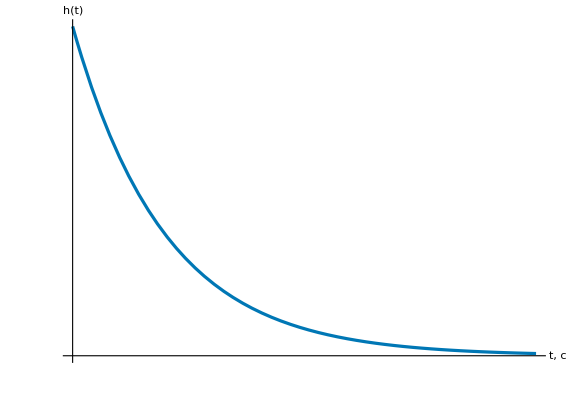

```mathematica
tickXStep =0.002;
tickYStep =100;
stepRespPic=Plot[{TFstep},{t, 0, maxt},
AxesStyle->Directive[Thickness[0.002],Black],
AxesLabel->{sizeText["t, с"], sizeText["h(t)"]},
GridLines->None,
AspectRatio->11/16,
PlotStyle->{{RGBColor["#0077b5"],Thickness[0.004]},{Black,dashingStyle}},
PlotRange->{{0,maxt},Automatic},
PlotRangeClipping->False,
ImageSize->Large,
Ticks->{
(#&@Array[{tickXStep#,,{0.006,0.006}}&,100]),
(#&@Array[{tickYStep #,,{0.006,0.006}}&,100])
}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"step.svg";
Export[fName,stepRespPic];
```

## Bode plot

### Log Plot

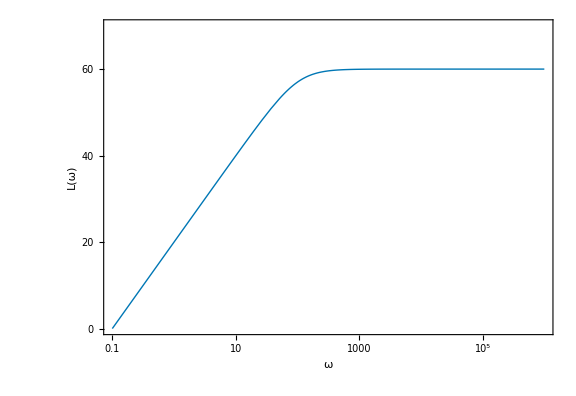

```mathematica
bodePlot=BodePlot[TF,{10^-1,10^6},
PlotRange->{{0,70},Automatic},
PlotStyle->Thickness[0.004],
ImageSize->Large,
PlotLayout->"List"
];
ampBodePlot=RestylePlot[
bodePlot[[1]],
{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"log-apm-freq.svg";
Export[fName,ampBodePlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\differential-with-delay\log-apm-freq.svg

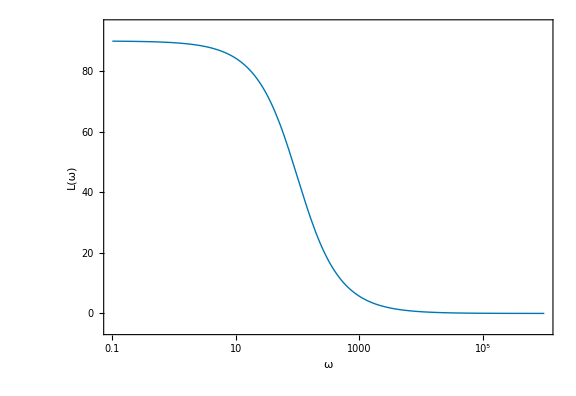

```mathematica
phaseBodePlot=RestylePlot[
bodePlot[[2]],
{RGBColor["#0077b5"],Thickness[0.004]},
PlotRange->{Automatic,{-5,95}},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"log-phase-freq.svg";
Export[fName,phaseBodePlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\differential-with-delay\log-phase-freq.svg

### Plot

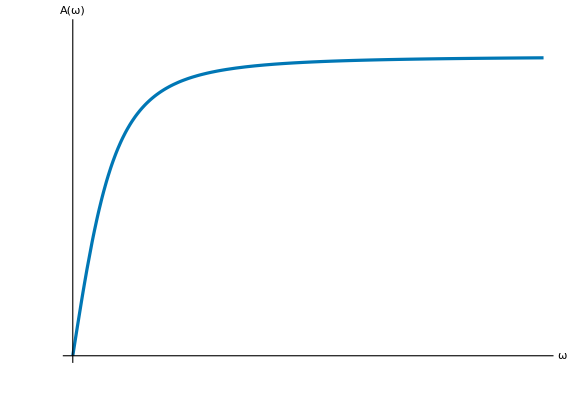

```mathematica
ampPlot=Plot[Abs[TF[I f]], {f,0, 1000},
PlotRange->{Automatic,{0,1100}},
PlotStyle->{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["A(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}},
Ticks->{
(#&@Array[{100#,,{0.006,0.006}}&,100]),
(#&@Array[{100#,,{0.006,0.006}}&,100])
}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"amp-freq.svg";
Export[fName,ampPlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\differential-with-delay\amp-freq.svg

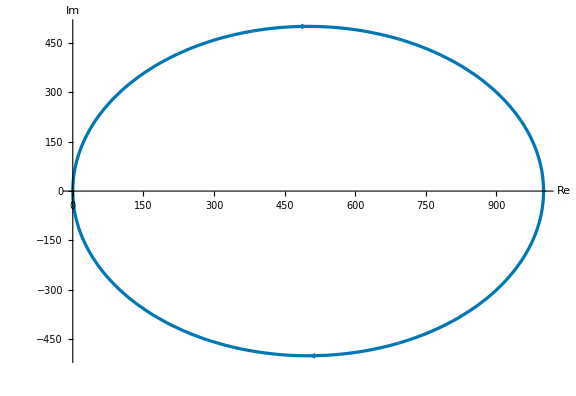

```mathematica
nyquistPlot=NyquistPlot[TF,
(*PlotRange->{{-0.05,.15},{-0.6,0.05}},*)
PlotStyle->{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["Re"],sizeText["Im"]},
AxesOrigin->{0,0},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"nyquist.svg";
Export[fName,nyquistPlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\differential-with-delay\nyquist.svg